# Analyzing the Potential

```mathematica
Clear["Global`*"]
```

```mathematica
(*Takayama's Master Thesis*)
(*μ=2.7*10^-3;M=1.6;m = 2; g = 1; v= 6.4*10^-4; n= 10; CN = 0.1; Subscript[σ, i]=0.8;*)
(*Paper FIG1(a)*)
μ=2.04*10^-3; M=1.17; m=2; g=2*10^-5; v=4.7*10^-4; n = 4; CN = 0.04; Subscript[σ, i] = 0.4;
(*Paper FIG(a) lower potential fit to Planck data *)
(*μ=(2.04*10^-3)/3; M=0.17; m=2; g=2*10^-5; v=(4.7*10^-4)/3; n = 4; CN = 0.04; Subscript[σ, i] = 0.07;*)

(*μ=2.0*10^-3;M=0.59; m = 2; g = 2.0*10^-5; v= 5.0*10^-4; n= 4; CN = 0.05; Subscript[σ, i] = 0.2;*)
Subscript[σ, c]= ((m*(3m-1))/((2m-1)*(m-1)))^((m-1)/(4m-2))*(2/(2m*(2m-1))^(m/(4m-2)))*(μ*M^(m-1))^(1/(2m-1)) ;(* The value of σ at the end of hybrid inflation *)
Subscript[σ, d]=  ((2m)/(2m-1))^((m-1)/(6m-4))*(4^(2m-1)/(2m*(2m-1))^m)^(1/(6m-4))*(μ*M^(m-1))^(1/(3m-2));
 Subscript[ϕ, init] = -v^2/μ^2*Subscript[σ, c]; (* The value of ϕ at the end of hybrid inflation *)

Subscript[ϕ, oscend] = -v^3/μ^3*Subscript[σ, c]; (* The value of ϕ at the end of oscillation period after hybrid inflation *)
Subscript[ϕ, oscendprecise] = Subscript[ϕ, oscend]*(Cos[Sqrt[5/3]*Log[μ/v]]+Sqrt[3/5]*Sin[Sqrt[5/3]*Log[μ/v]]);
(Cos[Sqrt[5/3]*Log[μ/v]]+Sqrt[3/5]*Sin[Sqrt[5/3]*Log[μ/v]])
Subscript[ψ, start]=  (4^m/((2m-1)*(2m)))^(1/(2m-2))*M*(μ/Subscript[σ, i])^(1/(m-1));
Subscript[ψ, end] = 2(μ*M^(m-1))^(1/m);

Subscript[ϕ, end] =  -√2*(v^2/g)^(1/n) ;(* The value of ϕ at the end of oscillation period after new inflation *)

VH[m_,M_,μ_, σ_,ψ_]:= ( -μ^2+ ψ^(2m)/(4^m*M^(2m-2)) )^2 * (1+σ^4/8+ψ^2/2)+ ((m^2*σ^2*ψ^2)/4^(2m-1))*(ψ/M)^(4m-4) + ((m * ψ^(2m) * σ^2)/(2^(2m-1)*M^(2m-2)))*(-μ^2+ ψ^(2m)/(4^m * M^(2m-2)) ) ;
(*VH[m_,M_,μ_, σ_,ψ_]:= ((m^2*σ^2*ψ^2)/4^(2m-1))*(ψ/M)^(4m-4) *)

VN[v_,ϕ_,g_, CN_, n_]:= (v^2  - g/2^(n/2)ϕ^n)^2-CN/2*v^4*ϕ^2;

VI[m_,M_,μ_, σ_,ψ_,ϕ_,v_] := ( -μ^2+ ψ^(2m)/(4^m*M^(2m-2)) )^2 * ϕ^2/2 -( -μ^2+ ψ^(2m)/(4^m*M^(2m-2)))*v^2*σ*ϕ;

VH[m,M,μ, 0,Subscript[ψ, end]]
VN[v,ϕ,g, CN, n];
VI[m,M,μ, σ,ψ,ϕ,v];
Nefold = Integrate[VH[m,M,μ, σ,Subscript[ψ, start]]/D[VH[m,M,μ, σ,Subscript[ψ, start]],σ],{σ,Subscript[σ, c],Subscript[σ, i]}];
Nefoldappr =  Integrate[2/σ^3,{σ,Subscript[σ, d],Subscript[σ, i]}]+ Integrate[ ((2m-1)/m)*((2m*(2m-1))^(m/(m-1))/4^((2m-1)/(m-1)))*(σ^((3m-1)/(m-1))/(μ^(2/(m-1))*M^2)),{σ,Subscript[σ, c],Subscript[σ, d]}];
Nefoldappr2 =((3m-2)/(2m-1))*((2m-1)/(2m))^((m-1)/(3m-2))*((2m*(2m-1))^(m/(3m-2))/4^((2m-1)/(3m-2)))*(μ*M^(m-1))^(-2/(3m-2));
Print["σ_c=",Subscript[σ, c]]
Print["σ_d=",Subscript[σ, d]]
Print["ψ_start=",Subscript[ψ, start]]
Print["ψ_end=",Subscript[ψ, end]]
Print["ϕ_init=",Subscript[ϕ, init]]
Print["ϕ_oscend=",Subscript[ϕ, oscend]]
Print["ϕ_oscendprecise=",Subscript[ϕ, oscendprecise]]
Print["ϕ_end=",Subscript[ϕ, end]]
Print["Nefold=",Nefold]
Print["Nefoldappr=",Nefoldappr]
Print["Nefoldappr2 =",Nefoldappr2 ]
{min,max}={10^-14,2*10^-11};

Show[
Plot3D[
VH[m,M,μ, σ,ψ](*+ VN[v,ϕ,g,CN,n] + VI[m,M,μ, σ,ψ,ϕ,v]*),{ψ,0,0.13},{σ,-0.2,0.8},ScalingFunctions->{"Reverse",None},PlotRange->{min,max}, AxesStyle->Directive[Black,FontSize->10],ColorFunction->(ColorData["SolarColors"][#3]&),ColorFunctionScaling->True,PlotLegends->BarLegend[{"SolarColors",{min,max}},LabelStyle->{Black}],Mesh -> 40, MeshStyle->Directive[Gray, Opacity[0.5]]
],

Graphics3D[Text[Style["ψ",16],Scaled[{0,-.15,0}]]],
Graphics3D[Text[Style["σ",16],Scaled[{1.1,1.1,0}]]],
Graphics3D[Text[Style["V",20],Scaled[{0,0,1.2}]]]
]
```

0.415517

0.

σ_c=0.142688

σ_d=0.207037

ψ_start=0.0068901

ψ_end=0.0977098

ϕ_init=-0.00757397

ϕ_oscend=-0.00174498

ϕ_oscendprecise=-0.000725071

ϕ_end=-0.458465

Nefold=42.3832

Nefoldappr=24.0225

Nefoldappr2 =31.1058

-Graphics3D-

# Zero mode EOM (by t)

```mathematica
Vbare[σ_,ψ_,ϕ_]:=VH[m,M,μ, σ,ψ]+VN[v,ϕ,g, CN, n]+VI[m,M,μ, σ,ψ,ϕ,v];
CNT = - Vbare[0,Subscript[ψ, end],Subscript[ϕ, end]];
V[ σ_,ψ_,ϕ_]:=Vbare[ σ,ψ,ϕ]+CNT;
Subscript[Γ, σ]=1*10^-11;Subscript[Γ, ψ]=1*10^-11;Subscript[Γ, ϕ]=1*10^-11;
ρ[ σ_,ψ_,ϕ_,rad_,t_] :=(D[σ,t]^2+D[ψ,t]^2+D[ϕ,t]^2)/2 + V[σ,ψ,ϕ]+rad;
p[ σ_,ψ_,ϕ_,rad_,t_] := (D[σ,t]^2+D[ψ,t]^2+D[ϕ,t]^2)/2 - V[σ,ψ,ϕ]+rad/3;
H[ σ_,ψ_,ϕ_,rad_,t_]:=Sqrt[ρ[ σ,ψ,ϕ,rad,t]/3];
Subscript[T, end]=10^8;
solution=NDSolve[
{
a''[t] == -(ρ[σ[t],ψ[t],ϕ[t],rad[t],t]+3p[σ[t],ψ[t],ϕ[t],rad[t],t])*a[t]/6,
(*a'[t]/a[t] == H[ σ[t],ψ[t],ϕ[t],rad[t],t],*)
D[(a[t]^4*rad[t]),t]/a[t]^4 == Subscript[Γ, σ]*σ'[t]^2+Subscript[Γ, ψ]*ψ'[t]^2+Subscript[Γ, ϕ]*ϕ'[t]^2,
σ''[t]+(3H[σ[t],ψ[t],ϕ[t],rad[t],t]+Subscript[Γ, σ])*σ'[t]+D[ V[σ[t],ψ[t],ϕ[t]],σ[t]] == 0,
ψ''[t]+(3H[σ[t],ψ[t],ϕ[t],rad[t],t]+Subscript[Γ, ψ])*ψ'[t]+D[ V[σ[t],ψ[t],ϕ[t]],ψ[t]] == 0,
ϕ''[t]+(3H[σ[t],ψ[t],ϕ[t],rad[t],t]+Subscript[Γ, ϕ])*ϕ'[t]+D[ V[σ[t],ψ[t],ϕ[t]],ϕ[t]] == 0,
Nefolds'[t] == H[σ[t],ψ[t],ϕ[t],rad[t],t],
σ[0]==Subscript[σ, i],ψ[0]==Subscript[ψ, start],ϕ[0]==Subscript[ϕ, init],σ'[0]==0,ψ'[0]==0,ϕ'[0]==0,rad[0]==0,a[0]==1,a'[0]==H[σ[0],ψ[0],ϕ[0],0,rad[0]],Nefolds[0]== Log[a[0]]-135.6},{a,σ,ψ,ϕ,rad,Nefolds},{t,0,Subscript[T, end]},MaxSteps->Infinity]
```

{{a→                                 8
InterpolatingFunction[{{0., 1. 10 }}, <>],σ→                                 8
InterpolatingFunction[{{0., 1. 10 }}, <>],ψ→                                 8
InterpolatingFunction[{{0., 1. 10 }}, <>],ϕ→                                 8
InterpolatingFunction[{{0., 1. 10 }}, <>],rad→                                 8
InterpolatingFunction[{{0., 1. 10 }}, <>],Nefolds→                                 8
InterpolatingFunction[{{0., 1. 10 }}, <>]}}

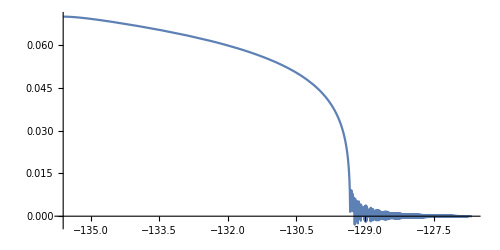

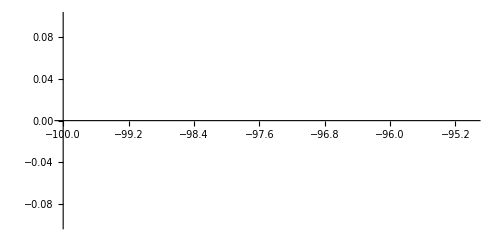

```mathematica
ParametricPlot[Evaluate[{Nefolds[t],σ[t]}/. solution],{t,0,Subscript[T, end]},AspectRatio -> 1/2,ImageSize->500]
ParametricPlot[Evaluate[{Nefolds[t],σ[t]}/. solution],{t,0,Subscript[T, end]},AspectRatio -> 1/2,ImageSize->500, PlotRange->{{-100,-95},{-0.1,0.1}}]
```

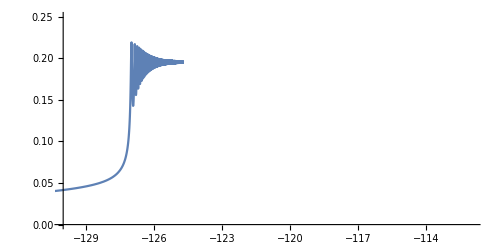

```mathematica
ParametricPlot[Evaluate[{Nefolds[t],ψ[t]}/. solution],{t,0,Subscript[T, end]},AspectRatio -> 1/2,ImageSize->500, PlotRange->{{-130,-112},{0,0.25}}]
```

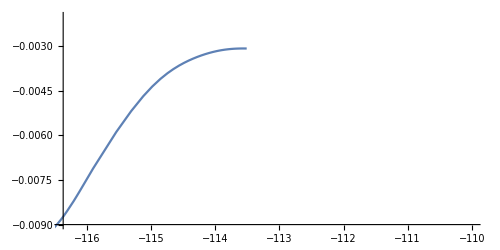

```mathematica
ParametricPlot[Evaluate[{Nefolds[t],ϕ[t]}/. solution],{t,0,Subscript[T, end]},AspectRatio -> 1/2,ImageSize->500, PlotRange->{{-116.369,-110},{-0.009,-0.002}}]
```

# Zero mode EOM (by N)

```mathematica
Vbare[σ_,ψ_,ϕ_]:=VH[m,M,μ, σ,ψ]+VN[v,ϕ,g, CN, n]+VI[m,M,μ, σ,ψ,ϕ,v];
CNT = - Vbare[0,Subscript[ψ, end],Subscript[ϕ, end]];
V[ σ_,ψ_,ϕ_]:=Vbare[ σ,ψ,ϕ]+CNT;
Subscript[Γ, σ]=1*10^-11;Subscript[Γ, ψ]=1*10^-11;Subscript[Γ, ϕ]=0;(*1*10^-11;*)
ρ[ σ_,ψ_,ϕ_,vsigma_, vpsi_, vphi_,rad_] :=(vsigma^2+vpsi^2+vphi^2)/2 + V[σ,ψ,ϕ]+rad;
p[ σ_,ψ_,ϕ_,vsigma_, vpsi_, vphi_,rad_] := (vsigma^2+vpsi^2+vphi^2)/2 - V[σ,ψ,ϕ]+rad/3;
H[ σ_,ψ_,ϕ_,vsigma_, vpsi_, vphi_,rad_]:=Sqrt[ρ[ σ,ψ,ϕ,vsigma,vpsi,vphi,rad]/3];
Subscript[Nefolds, init]= -135.6;
Subscript[Nefolds, end]=-110;

solution=NDSolve[
{

rad'[Nefolds]== -4 rad[Nefolds]+(Subscript[Γ, σ]*vsigma[Nefolds]^2+Subscript[Γ, ψ]*vpsi[Nefolds]^2+Subscript[Γ, ϕ]*vphi[Nefolds]^2)/H[ σ[Nefolds],ψ[Nefolds],ϕ[Nefolds],vsigma[Nefolds], vpsi[Nefolds], vphi[Nefolds],rad[Nefolds]],

vsigma'[Nefolds]==-3vsigma[Nefolds]- (D[ V[σ[Nefolds],ψ[Nefolds],ϕ[Nefolds]],σ[Nefolds]]+Subscript[Γ, σ]*vsigma[Nefolds])/H[ σ[Nefolds],ψ[Nefolds],ϕ[Nefolds],vsigma[Nefolds], vpsi[Nefolds], vphi[Nefolds],rad[Nefolds]],

vpsi'[Nefolds]==-3vpsi[Nefolds]- (D[ V[σ[Nefolds],ψ[Nefolds],ϕ[Nefolds]],ψ[Nefolds]]+Subscript[Γ, ψ]*vpsi[Nefolds])/H[ σ[Nefolds],ψ[Nefolds],ϕ[Nefolds],vsigma[Nefolds], vpsi[Nefolds], vphi[Nefolds],rad[Nefolds]],

vphi'[Nefolds]==-3vphi[Nefolds]- (D[ V[σ[Nefolds],ψ[Nefolds],ϕ[Nefolds]],ϕ[Nefolds]]+Subscript[Γ, ϕ]*vphi[Nefolds])/H[ σ[Nefolds],ψ[Nefolds],ϕ[Nefolds],vsigma[Nefolds], vpsi[Nefolds], vphi[Nefolds],rad[Nefolds]],

σ'[Nefolds] ==vsigma[Nefolds]/H[ σ[Nefolds],ψ[Nefolds],ϕ[Nefolds],vsigma[Nefolds], vpsi[Nefolds], vphi[Nefolds],rad[Nefolds]],

ψ'[Nefolds]==vpsi[Nefolds]/H[ σ[Nefolds],ψ[Nefolds],ϕ[Nefolds],vsigma[Nefolds], vpsi[Nefolds], vphi[Nefolds],rad[Nefolds]] ,

 ϕ'[Nefolds]==vphi[Nefolds]/H[ σ[Nefolds],ψ[Nefolds],ϕ[Nefolds],vsigma[Nefolds], vpsi[Nefolds], vphi[Nefolds],rad[Nefolds]],

σ[Subscript[Nefolds, init]]==Subscript[σ, i],ψ[Subscript[Nefolds, init]]==Subscript[ψ, start],ϕ[Subscript[Nefolds, init]]==Subscript[ϕ, init],vsigma[Subscript[Nefolds, init]]==0,vpsi[Subscript[Nefolds, init]]==0,vphi[Subscript[Nefolds, init]]==0,rad[Subscript[Nefolds, init]]==0},{σ,ψ,ϕ,vsigma,vpsi,vphi,rad},{Nefolds,Subscript[Nefolds, init],Subscript[Nefolds, end]},MaxSteps->Infinity,Method->Automatic]
```

{{σ→InterpolatingFunction[…],ψ→InterpolatingFunction[…],ϕ→InterpolatingFunction[…],vsigma→InterpolatingFunction[…],vpsi→InterpolatingFunction[…],vphi→InterpolatingFunction[…],rad→InterpolatingFunction[…]}}

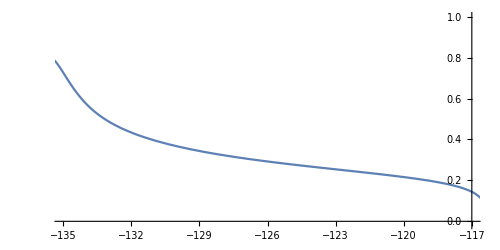

```mathematica
Plot[Evaluate[σ[Nefolds]/. solution],{Nefolds,Subscript[Nefolds, init],Subscript[Nefolds, end]},AspectRatio -> 1/2,ImageSize->500, PlotRange->{{-135.,-117},{-0.016,1}}]
```

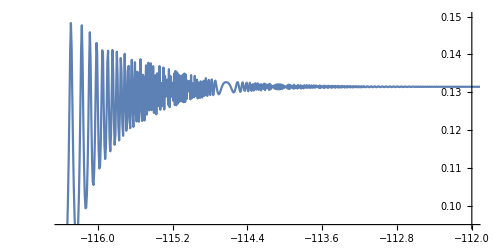

```mathematica
Plot[Evaluate[ψ[Nefolds]/. solution],{Nefolds,Subscript[Nefolds, init],Subscript[Nefolds, end]},AspectRatio -> 1/2,ImageSize->500, PlotRange->{{-116.369,-112},{0.095,0.15}}]
```

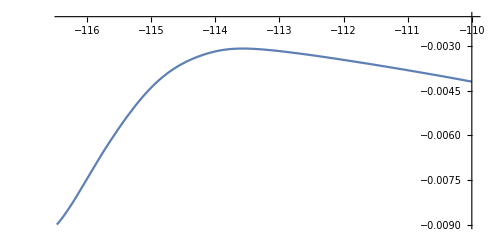

```mathematica
Plot[Evaluate[ϕ[Nefolds]/. solution],{Nefolds,Subscript[Nefolds, init],Subscript[Nefolds, end]},AspectRatio -> 1/2,ImageSize->500, PlotRange->{{-116.369,-110},{-0.009,-0.002}}]
```

```mathematica
mσ2 = D[ V[σ[Nefolds],ψ[Nefolds],ϕ[Nefolds]],{σ[Nefolds],2}];
mψ2 = D[ V[σ[Nefolds],ψ[Nefolds],ϕ[Nefolds]],{ψ[Nefolds],2}];
mϕ2 = D[ V[σ[Nefolds],ψ[Nefolds],ϕ[Nefolds]],{ϕ[Nefolds],2}];
H2 = H[ σ[Nefolds],ψ[Nefolds],ϕ[Nefolds],vsigma[Nefolds], vpsi[Nefolds], vphi[Nefolds],rad[Nefolds]]^2;
```

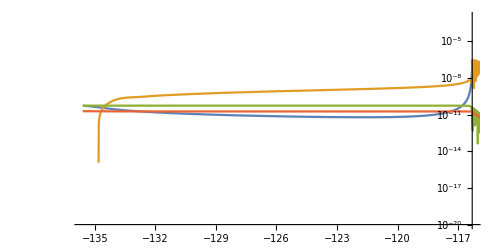

```mathematica
LogPlot[{Evaluate[mσ2/. solution],Evaluate[mψ2/. solution],Evaluate[mϕ2/. solution],Evaluate[H2 /. solution]},{Nefolds,Subscript[Nefolds, init],Subscript[Nefolds, end]},AspectRatio -> 1/2,ImageSize->500, PlotRange->{{-135.6,-116.3},{10^(-20),10^(-3)}}]
```

# Important Parameters

## Effective Masses

```mathematica
Subscript[m, σ] = √((8 μ^3)/M)
Subscript[m, ψ] = √((8 μ^3)/M+16 μ^4)
```

0.000313712

0.000315064

## Field Values

```mathematica
Subscript[ϕ, init] = -v^3/μ^3*Subscript[σ, c]
Subscript[ϕ, 0] = -v^2/μ^2*Subscript[σ, c]
Subscript[ϕ, min] = N[-√2*(v^2/g)^(1/n)]
Subscript[ψ, end] = 2(μ*M^(m-1))^(1/m)
VH[m,M,μ, 0,Subscript[ψ, end]]+
VN[v,Subscript[ϕ, min],g, CN, n]+
VI[m,M,μ, 0,Subscript[ψ, end],Subscript[ϕ, min],v]
```

-0.00231593

-0.00977034

-0.324901

0.131453

-8.85507×10^-16

```mathematica
√(D[VH[m,M,μ, σ,Subscript[ψ, end]],{σ,2}]/. σ -> 0)
```

0.000313712

```mathematica
Subscript[a, osc] = -114.5;
Subscript[k, peak] = Exp[Subscript[a, osc]]*0.3*Subscript[m, σ]
```

1.76577×10^-54

## Perturbation EOM

```mathematica
F[Φ_] :=Sqrt[(1-2Φ)*(1+2Φ)^3] 
G[Φ_] :=D[F[Φ],Φ]
H[Φ_] :=D[F[Φ],Φ,Φ]
```

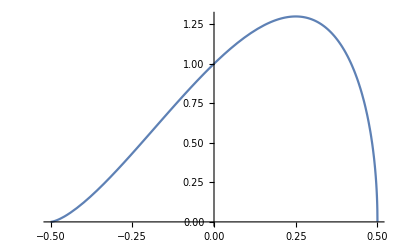

```mathematica
Plot[F[Φ],{Φ,-1/2,1/2}]
```

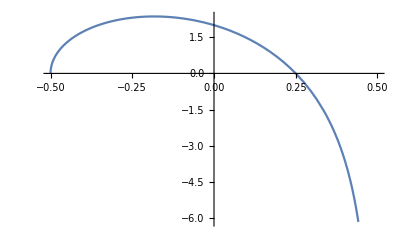

```mathematica
Plot[Evaluate@G[Φ],{Φ,-1/2,1/2}]
```

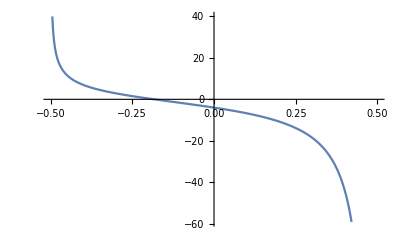

```mathematica
Plot[Evaluate@H[Φ],{Φ,-1/2,1/2}]
```

```mathematica
F[Φ]
G[Φ]
H[Φ]
Together[G[Φ]]
Together[H[Φ]]
```

√((1-2 Φ) (1+2 Φ)^3)

(6 (1-2 Φ) (1+2 Φ)^2-2 (1+2 Φ)^3)/(2 √((1-2 Φ) (1+2 Φ)^3))

(24 (1-2 Φ) (1+2 Φ)-24 (1+2 Φ)^2)/(2 √((1-2 Φ) (1+2 Φ)^3))-((6 (1-2 Φ) (1+2 Φ)^2-2 (1+2 Φ)^3)^2)/(4 ((1-2 Φ) (1+2 Φ)^3)^(3/2))

-(2 (-1+12 Φ^2+16 Φ^3))/(√(-((-1+2 Φ) (1+2 Φ)^3)))

-(4 (1+2 Φ) (-1-4 Φ+8 Φ^2))/((-1+2 Φ) √(-((-1+2 Φ) (1+2 Φ)^3)))

```mathematica
F[Φ]/G[Φ]
H[Φ]/G[Φ]
Together[F[Φ]/G[Φ]]
Together[H[Φ]/G[Φ]]
```

(2 (1-2 Φ) (1+2 Φ)^3)/(6 (1-2 Φ) (1+2 Φ)^2-2 (1+2 Φ)^3)

(2 √((1-2 Φ) (1+2 Φ)^3) ((24 (1-2 Φ) (1+2 Φ)-24 (1+2 Φ)^2)/(2 √((1-2 Φ) (1+2 Φ)^3))-((6 (1-2 Φ) (1+2 Φ)^2-2 (1+2 Φ)^3)^2)/(4 ((1-2 Φ) (1+2 Φ)^3)^(3/2))))/(6 (1-2 Φ) (1+2 Φ)^2-2 (1+2 Φ)^3)

((-1+2 Φ) (1+2 Φ))/(2 (-1+4 Φ))

(2 (-1-4 Φ+8 Φ^2))/((-1+2 Φ) (1+2 Φ) (-1+4 Φ))

## σ_c behavior

```mathematica
Subscript[σ, c][m_,μ_,M_]:= ((m*(3m-1))/((2m-1)*(m-1)))^((m-1)/(4m-2))*(2/(2m*(2m-1))^(m/(4m-2)))*(μ*M^(m-1))^(1/(2m-1))
```

```mathematica
μ=2.7*10^-3;M=1.6; 
Plot3D[Subscript[σ, c][m,μ,M],{m,2,10},{μ,10^-3,10^-2}]
```

-Graphics3D-

## Calculating potential variables from observation variables

### Previous Research (WMAP)

```mathematica
R = 4.7*10^-5; (*amplitude of curvature perturbation*)

(*sigma*)
sigma[ns_ , nsrun_, m_ ] :=1/(2^(3/4)√(3*(3m-2)))*((25 m^2-34m+13)*(ns-1)^2-12(3m-1)*(m-1)*nsrun +(7m-5)(ns-1)√((m+1)^2(ns-1)^2-24(3m-1)*(m-1)*nsrun))^(1/4)
(*sigma_d*)
sigmad[ns_ , nsrun_, m_ ]:=((m-1)/(3m-1)*(3 sigma[ns, nsrun, m ]^2-ns+1))^((m-1)/(6m-4))*(sigma[ns , nsrun, m])^((2m-1)/(3m-2))
(*mu*)
mu[ns_ , nsrun_, m_ ]:=√(√3*Pi*R*(sigmad[ns, nsrun, m ]^3*(sigmad[ns , nsrun, m ]/sigma[ns , nsrun, m ])^((3m-1)/(m-1))+ sigma[ns, nsrun, m ]^3))
(*M*)
M[ns_ , nsrun_, m_]:=( sigmad[ns , nsrun, m ]^(3m-2)/mu[ns , nsrun, m ] *((2m-1)/(2m))^((m-1)/2)*((2m*(2m-1))^m/4^(2m-1))^(1/2))^(1/(m-1))
(*Subscript[σ, c]*)
sigmac[ns_ , nsrun_, m_]:= ((m*(3m-1))/((2m-1)*(m-1)))^((m-1)/(4m-2))*(2/(2m*(2m-1))^(m/(4m-2)))*(mu[ns , nsrun, m ]*(M[ns , nsrun, m])^(m-1))^(1/(2m-1)) 
psistart[ns_ , nsrun_, m_]:= (4^m/((2m-1)*(2m)))^(1/(2m-2))*M[ns , nsrun, m]*(mu[ns , nsrun, m ]/sigma[ns , nsrun, m ])^(1/(m-1));
psiend[ns_ , nsrun_, m_] := 2(mu[ns , nsrun, m ]*M[ns , nsrun, m]^(m-1))^(1/m);

VH[ns_ , nsrun_, m_, σ_,ψ_]:= ( -mu[ns , nsrun, m ]^2+ ψ^(2m)/(4^m*M[ns , nsrun, m]^(2m-2)) )^2 * (1+σ^4/8+ψ^2/2)+ ((m^2*σ^2*ψ^2)/4^(2m-1))*(ψ/M[ns , nsrun, m])^(4m-4) + ((m * ψ^(2m) * σ^2)/(2^(2m-1)*M[ns , nsrun, m]^(2m-2)))*(-mu[ns , nsrun, m ]^2+ ψ^(2m)/(4^m * M[ns , nsrun, m]^(2m-2)) ) 

Nr1[ns_ , nsrun_, m_] := NIntegrate[VH[ns , nsrun, m, σ, psistart[ns , nsrun, m]]/D[VH[ns, nsrun, m, σ, psistart[ns , nsrun, m]],σ],{σ,sigmac[ns , nsrun, m ],sigma[ns , nsrun, m ]}];
Nr2[ns_ , nsrun_, m_] :=  NIntegrate[2/σ^3,{σ,sigmad[ns , nsrun, m],sigma[ns , nsrun, m ]}]+ NIntegrate[ ((2m-1)/m)*((2m*(2m-1))^(m/(m-1))/4^((2m-1)/(m-1)))*(σ^((3m-1)/(m-1))/(mu[ns , nsrun, m ]^(2/(m-1))*M[ns , nsrun, m]^2)),{σ,sigmac[ns , nsrun, m ],sigmad[ns , nsrun, m]}];
Nr3[ns_ , nsrun_, m_] :=((3m-2)/(2m-1))*((2m-1)/(2m))^((m-1)/(3m-2))*((2m*(2m-1))^(m/(3m-2))/4^((2m-1)/(3m-2)))*(mu[ns , nsrun, m ]*M[ns , nsrun, m]^(m-1))^(-2/(3m-2));
```

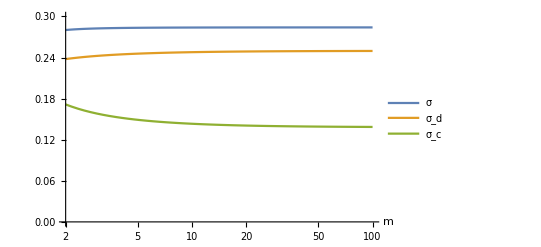

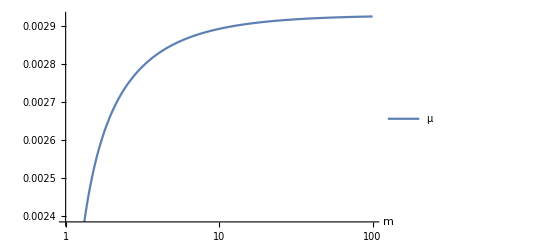

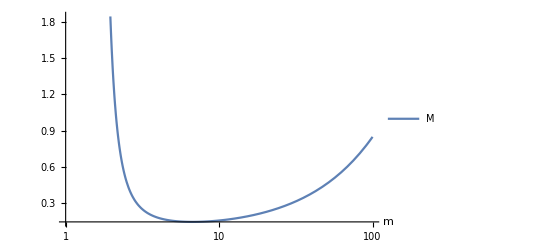

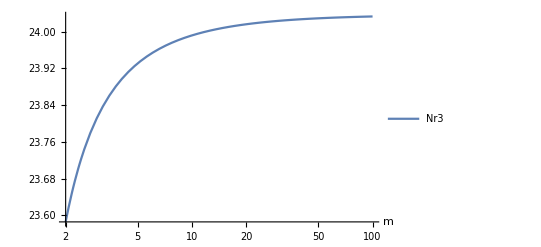

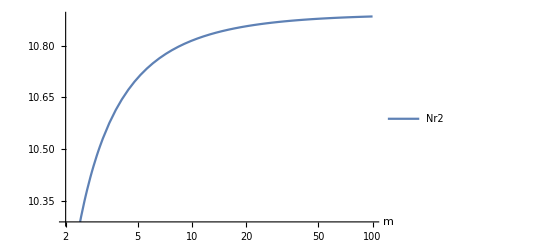

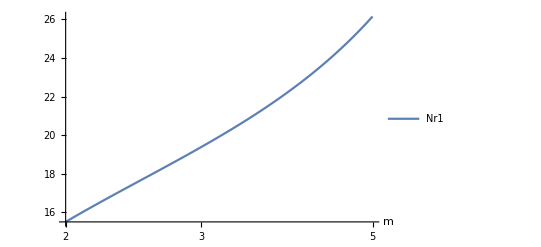

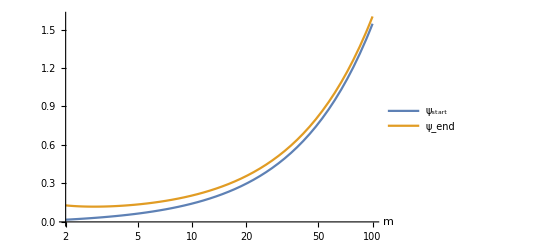

```mathematica
ns = 1.13; nsrun = -0.055;
LogLinearPlot[{sigma[ns, nsrun, m ],sigmad[ns, nsrun, m ],sigmac[ns, nsrun, m ]} ,{m,2,100},PlotRange->{0,0.3},AxesLabel->{"m"},PlotLegends->{"σ","σ_d","σ_c"}]
LogLinearPlot[mu[ns , nsrun, m ] ,{m,1,100},AxesLabel->{"m"},PlotLegends->{μ}]
LogLinearPlot[M[ns , nsrun, m ] ,{m,1,100},AxesLabel->{"m"},PlotLegends->{M}]
LogLinearPlot[Nr3[ns, nsrun, m ] ,{m,2,100},AxesLabel->{"m"},PlotLegends->{Nr3}]
LogLinearPlot[Nr2[ns, nsrun, m ] ,{m,2,100},AxesLabel->{"m"},PlotLegends->{Nr2}]
LogLinearPlot[Nr1[ns, nsrun, m ] ,{m,2,5},AxesLabel->{"m"},PlotLegends->{Nr1}]
(*LogLinearPlot[{Nr1[ns, nsrun, m ],Nr2[ns, nsrun, m ],Nr3[ns, nsrun, m ]} ,{m,2,100},AxesLabel->{"m"},PlotLegends->{Nr1,Nr2,Nr3}]*)
LogLinearPlot[{psistart[ns, nsrun, m ],psiend[ns, nsrun, m ]} ,{m,2,100},AxesLabel->{"m"},PlotLegends->{"ψ_start","ψ_end"}]
(*LogLinearPlot[psiend[ns, nsrun, m ] ,{m,2,100},AxesLabel->{"m"},PlotLegends->{Subscript[ψ, end]}]*)
```

```mathematica
ns = 1.13; nsrun = -0.055;m =2;
```

```mathematica
Print["σ = ",sigma[ns , nsrun, m ]", σ_d = ",sigmad[ns , nsrun, m]", σ_c = ",sigmac[ns , nsrun, m]", μ = ",mu[ns , nsrun, m ]", M = ",M[ns , nsrun, m ]]
Print["ψ_start= ",psistart[ns , nsrun, m]", ψ_end = ",psiend[ns , nsrun, m]]
Print["Nr1 = ",Nr1[ns , nsrun, m ]", Nr2 = ",Nr2[ns , nsrun, m ]", Nr3 = ",Nr3[ns , nsrun, m ]]
```

σ = 0.280196 , σ_d = 0.237765 , σ_c = 0.171601 , μ = 0.00263784 , M = 1.57385

ψ_start= 0.0171088 , ψ_end = 0.128865

Nr1 = 15.5021 , Nr2 = 10.0148 , Nr3 = 23.5854

```mathematica
ClearAll["Global`*"]
```

### Planck Data

```mathematica
R = Sqrt[Exp[3.044]*10^-10] (*amplitude of curvature perturbation*)

(*sigma*)
sigma[ns_ , nsrun_, m_ ] :=1/(2^(3/4)√(3*(3m-2)))*((25 m^2-34m+13)*(ns-1)^2-12*(3m-1)*(m-1)*nsrun +(7m-5)(ns-1)√((m+1)^2(ns-1)^2-24*(3m-1)*(m-1)*nsrun))^(1/4);
(*sigma_d*)
sigmad[ns_ , nsrun_, m_ ]:=((m-1)/(3m-1)*(3 sigma[ns, nsrun, m ]^2-ns+1))^((m-1)/(6m-4))*(sigma[ns , nsrun, m])^((2m-1)/(3m-2));
(*mu*)
mu[ns_ , nsrun_, m_ ]:=√(√3*Pi*R*(sigmad[ns, nsrun, m ]^3*(sigmad[ns , nsrun, m ]/sigma[ns , nsrun, m ])^((3m-1)/(m-1))+ sigma[ns, nsrun, m ]^3));
(*M*)
M[ns_ , nsrun_, m_]:=( sigmad[ns , nsrun, m ]^(3m-2)/mu[ns , nsrun, m ] *((2m-1)/(2m))^((m-1)/2)*((2m*(2m-1))^m/4^(2m-1))^(1/2))^(1/(m-1));
(*Subscript[σ, c]*)
sigmac[ns_ , nsrun_, m_]:= ((m*(3m-1))/((2m-1)*(m-1)))^((m-1)/(4m-2))*(2/(2m*(2m-1))^(m/(4m-2)))*(mu[ns , nsrun, m ]*(M[ns , nsrun, m])^(m-1))^(1/(2m-1)) 
psistart[ns_ , nsrun_, m_]:= (4^m/((2m-1)*(2m)))^(1/(2m-2))*M[ns , nsrun, m]*(mu[ns , nsrun, m ]/sigma[ns , nsrun, m ])^(1/(m-1));
psiend[ns_ , nsrun_, m_] := 2(mu[ns , nsrun, m ]*M[ns , nsrun, m]^(m-1))^(1/m);

VH[ns_ , nsrun_, m_, σ_,ψ_]:= ( -mu[ns , nsrun, m ]^2+ ψ^(2m)/(4^m*M[ns , nsrun, m]^(2m-2)) )^2 * (1+σ^4/8+ψ^2/2)+ ((m^2*σ^2*ψ^2)/4^(2m-1))*(ψ/M[ns , nsrun, m])^(4m-4) + ((m * ψ^(2m) * σ^2)/(2^(2m-1)*M[ns , nsrun, m]^(2m-2)))*(-mu[ns , nsrun, m ]^2+ ψ^(2m)/(4^m * M[ns , nsrun, m]^(2m-2)) ) 

Nr1[ns_ , nsrun_, m_]:= NIntegrate[VH[ns , nsrun, m, σ, psistart[ns , nsrun, m]]/D[VH[ns, nsrun, m, σ, psistart[ns , nsrun, m]],σ],{σ,sigmac[ns , nsrun, m ],sigma[ns , nsrun, m ]}];
Nr2[ns_ , nsrun_, m_] :=  Integrate[2/σ^3,{σ,sigmad[ns , nsrun, m],sigma[ns , nsrun, m ]}]+ Integrate[ ((2m-1)/m)*((2m*(2m-1))^(m/(m-1))/4^((2m-1)/(m-1)))*(σ^((3m-1)/(m-1))/(mu[ns , nsrun, m ]^(2/(m-1))*M[ns , nsrun, m]^2)),{σ,sigmac[ns , nsrun, m ],sigmad[ns , nsrun, m]}];
Nr3[ns_ , nsrun_, m_] :=((3m-2)/(2m-1))*((2m-1)/(2m))^((m-1)/(3m-2))*((2m*(2m-1))^(m/(3m-2))/4^((2m-1)/(3m-2)))*(mu[ns , nsrun, m ]*M[ns , nsrun, m]^(m-1))^(-2/(3m-2));
```

0.0000458138

SetDelayed::write: 11.7[ns_,nsrun_,m_]のタグRealはProtectedです．

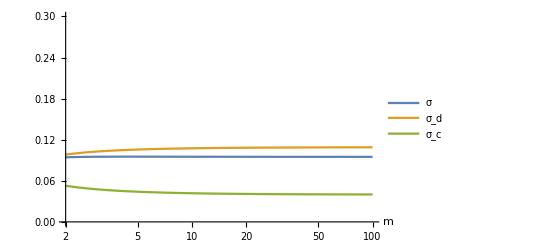

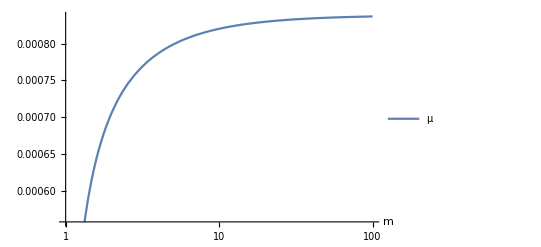

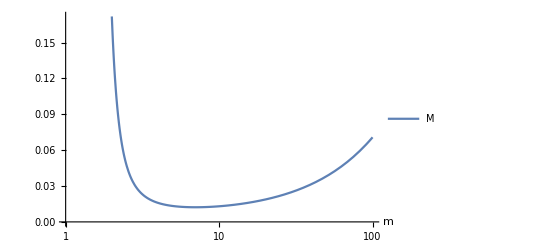

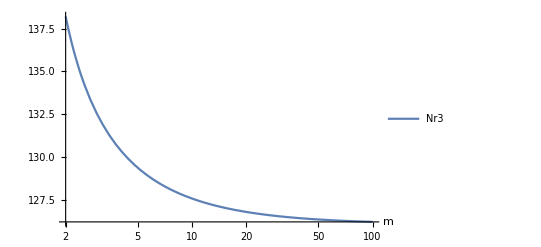

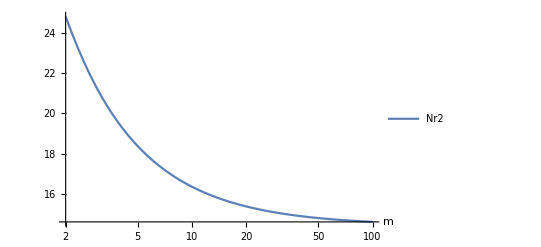

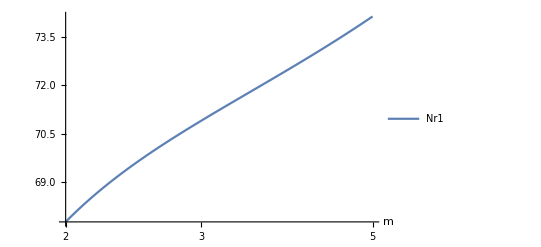

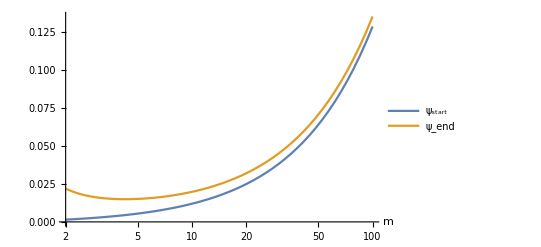

```mathematica
ns = 0.9649; nsrun = -0.0045;
LogLinearPlot[{sigma[ns, nsrun, m ],sigmad[ns, nsrun, m ],sigmac[ns, nsrun, m ]} ,{m,2,100},PlotRange->{0,0.3},AxesLabel->{"m"},PlotLegends->{"σ","σ_d","σ_c"}]
LogLinearPlot[mu[ns , nsrun, m ] ,{m,1,100},AxesLabel->{"m"},PlotLegends->{μ}]
LogLinearPlot[M[ns , nsrun, m ] ,{m,1,100},AxesLabel->{"m"},PlotLegends->{M}]
LogLinearPlot[Nr3[ns, nsrun, m ] ,{m,2,100},AxesLabel->{"m"},PlotLegends->{Nr3}]
LogLinearPlot[Nr2[ns, nsrun, m ] ,{m,2,100},AxesLabel->{"m"},PlotLegends->{Nr2}]
LogLinearPlot[Nr1[ns, nsrun, m ] ,{m,2,5},AxesLabel->{"m"},PlotLegends->{Nr1}]
(*LogLinearPlot[{Nr1[ns, nsrun, m ],Nr2[ns, nsrun, m ],Nr3[ns, nsrun, m ]} ,{m,2,100},AxesLabel->{"m"},PlotLegends->{Nr1,Nr2,Nr3}]*)
LogLinearPlot[{psistart[ns, nsrun, m ],psiend[ns, nsrun, m ]} ,{m,2,100},AxesLabel->{"m"},PlotLegends->{"ψ_start","ψ_end"}]
(*LogLinearPlot[psiend[ns, nsrun, m ] ,{m,2,100},AxesLabel->{"m"},PlotLegends->{Subscript[ψ, end]}]*)
```

```mathematica
m = 2;
Print["σ = ",sigma[ns , nsrun, m ]", σ_d = ",sigmad[ns , nsrun, m]", σ_c = ",sigmac[ns , nsrun, m]", μ = ",mu[ns , nsrun, m ]", M = ",M[ns , nsrun, m ]]
Print["ψ_start= ",psistart[ns , nsrun, m]", ψ_end = ",psiend[ns , nsrun, m]]
Print["Nr1 = ",Nr1[ns , nsrun, m ]", Nr2 = ",Nr2[ns , nsrun, m ]", Nr3 = ",Nr3[ns , nsrun, m ]]
```

σ = 0.0942573 , σ_d = 0.0982195 , σ_c = 0.0527943 , μ = 0.000706379 , M = 0.171149

ψ_start= 0.00148104 , ψ_end = 0.0219905

Power::infy: 無限式1/0が見付かりました．

Infinity::indet: 不定式0 ComplexInfinityが見付かりました．

Nr1 = 67.7477 , Nr2 = 24.8217 , Nr3 = 138.211

## Range of parameters in the case of Planck data

### Use data of TT,TE,EE+lowE+lensing (eq (13) and eq (15))

```mathematica
(*sigma*)
sigma[ns_ , nsrun_, m_ ] :=1/(2^(3/4)√(3*(3m-2)))*((25 m^2-34m+13)*(ns-1)^2-12*(3m-1)*(m-1)*nsrun +(7m-5)(ns-1)√((m+1)^2(ns-1)^2-24*(3m-1)*(m-1)*nsrun))^(1/4)/; nsrun ≥ ((m+1)^2(ns-1)^2)/(24*(3m-1)*(m-1))

(*sigma_d*)
sigmad[ns_ , nsrun_, m_ ]:=((m-1)/(3m-1)*(3 sigma[ns, nsrun, m ]^2-ns+1))^((m-1)/(6m-4))*(sigma[ns , nsrun, m])^((2m-1)/(3m-2))
```

```mathematica
nsmean = 0.9649; nsonesigma = 0.0042;
nsmin = nsmean -nsonesigma; nsmax =nsmean +nsonesigma;
Print["Data of TT,TE,EE+lowE+lensing \n ns:"]
Print["mean = ", nsmean,"  min = ", nsmin,"  max = ", nsmax]

nsrunmean = −0.0045; nsrunonesigma = 0.0067;
nsrunmin = nsrunmean -nsrunonesigma; nsrunmax =nsrunmean +nsrunonesigma;
Print["\n Data of TT,TE,EE+lowE+lensing \n ns_run:"]
Print["mean = ", nsrunmean,"  min = ", nsrunmin,"  max = ", nsrunmax]

mvar = 2;

(*Value inside of square root must be greater than zero
(m+1)^2(ns-1)^2≥24*(3m-1)*(m-1)*nsrun
*)
nsrunmaxconstraintmax = ((mvar+1)^2(nsmax-1)^2)/(24*(3mvar-1)*(mvar-1))
nsrunmaxconstraintmin= ((mvar+1)^2(nsmin-1)^2)/(24*(3mvar-1)*(mvar-1))
(*Print["nsrunmaxconstraint:", nsrunmaxconstraint]

nsrunmaxfinal =If[nsrunmaxconstraint<nsrunmax,nsrunmaxconstraint,nsrunmax];
Print["nsrunmaxfinal:", nsrunmaxfinal]*)

Plot3D[sigma[nsvar , nsrunvar, mvar ],{nsvar,nsmin,nsmax},{nsrunvar,nsrunmin,nsrunmax}]

FindMaximum[{sigma[nsvar,nsrunvar, mvar ],nsmax≥nsvar && nsvar≥nsmin && nsrunmean≥nsrunvar && nsrunvar≥nsrunmin},{nsvar,nsrunvar}]
FindMinimum[{sigma[nsvar,nsrunvar,mvar ],nsmax≥nsvar && nsvar≥nsmin && nsrunmaxconstraintmin≥nsrunvar && nsrunvar≥nsrunmean},{nsvar,nsrunvar}]

Plot3D[sigmad[nsvar , nsrunvar, mvar ],{nsvar,nsmin,nsmax},{nsrunvar,nsrunmin,nsrunmax}]

FindMaximum[{sigmad[nsvar,nsrunvar, mvar ],nsmax≥nsvar && nsvar≥nsmin && nsrunmean≥nsrunvar && nsrunvar≥nsrunmin},{nsvar,nsrunvar}]
FindMinimum[{sigmad[nsvar,nsrunvar,mvar ],nsmax≥nsvar && nsvar≥nsmin && nsrunmaxconstraintmin≥nsrunvar && nsrunvar≥nsrunmean},{nsvar,nsrunvar}]
```

Data of TT,TE,EE+lowE+lensing 
 ns:

mean = 0.9649  min = 0.9607  max = 0.9691

Data of TT,TE,EE+lowE+lensing 
 ns_run:

mean = -0.0045  min = -0.0112  max = 0.0022

0.0000716108

0.000115837

-Graphics3D-

{0.135778,{nsvar→0.9691,nsrunvar→-0.0112}}

FindMinimum::nrnum: 関数の値6.22937×10^-6+6.22937×10^-6 ⅈは{nsvar,nsrunvar} = {0.967865,-0.000619589}において実数ではありません．

General::stop: この計算中に，FindMinimum::nrnumのこれ以上の出力は表示されません．

FindMinimum::eit: アルゴリズムは500回の反復では許容範囲1.×10^-6に収束しませんでした．求められた最適な残差である，{6.00856×10^-22,66.0945,2.32758×10^-22}の{実行可能残差, KKT残差, 付加残差}が返されます．

{0.00131747,{nsvar→0.968174,nsrunvar→-0.000608146}}

-Graphics3D-

{0.134646,{nsvar→0.9691,nsrunvar→-0.0112}}

FindMinimum::cvmit: 500回以内の反復では要求された精度または確度に収束することができませんでした．

{0.,{nsvar→0.966318,nsrunvar→-0.000680677}}

```mathematica
(*amplitude of curvature perturbation*)

Rexpmean = 3.044; Rexponesigma = 0.014;
Rexpmin = Rexpmean - Rexponesigma; Rexpmax = Rexpmean + Rexponesigma;
Print["Data of TT,TE,EE+lowE+lensing \n ln(10^10A_s):"]
(*Print["Data of TT,TE,EE+lowE+lensing \n ln10^10A_s:"];*)
Print["mean = ", Rexpmean,"  min = ", Rexpmin,"  max = ", Rexpmax];
Rmean = Sqrt[Exp[Rexpmean]*10^-10];
Rmin =  Sqrt[Exp[Rexpmin]*10^-10];
Rmax =  Sqrt[Exp[Rexpmax]*10^-10];
Print["Data of TT,TE,EE+lowE+lensing \n A_s:"]
Print["mean = ", ScientificForm[Rmean],"  min = ", ScientificForm[Rmin], "  max = ", ScientificForm[Rmax]]


(*mu*)
mu[ns_ , nsrun_, m_ ,R_]:=√(√3*Pi*R*(sigmad[ns, nsrun, m ]^3*(sigmad[ns , nsrun, m ]/sigma[ns , nsrun, m ])^((3m-1)/(m-1))+ sigma[ns, nsrun, m ]^3))

Rvar = Rmean;
Print["R: mean = ", ScientificForm[Rvar]]
Plot3D[mu[nsvar , nsrunvar, mvar ,Rvar],{nsvar,nsmin,nsmax},{nsrunvar,nsrunmin,nsrunmax}]
FindMaximum[{mu[nsvar , nsrunvar, mvar ,Rvar],nsmax≥nsvar && nsvar≥nsmin && nsrunmean≥nsrunvar && nsrunvar≥nsrunmin},{nsvar,nsrunvar}]
FindMinimum[{mu[nsvar , nsrunvar, mvar ,Rvar],nsmax≥nsvar && nsvar≥nsmin && nsrunmaxconstraintmax≥nsrunvar && nsrunvar≥nsrunmean},{nsvar,nsrunvar}]

Rvar = Rmin;
Print["R: min = ", ScientificForm[Rvar]]
Plot3D[mu[nsvar , nsrunvar, mvar ,Rvar],{nsvar,nsmin,nsmax},{nsrunvar,nsrunmin,nsrunmax}]
FindMaximum[{mu[nsvar , nsrunvar, mvar ,Rvar],nsmax≥nsvar && nsvar≥nsmin && nsrunmean≥nsrunvar && nsrunvar≥nsrunmin},{nsvar,nsrunvar}]
FindMinimum[{mu[nsvar , nsrunvar, mvar ,Rvar],nsmax≥nsvar && nsvar≥nsmin && nsrunmaxconstraintmax≥nsrunvar && nsrunvar≥nsrunmean},{nsvar,nsrunvar}]

Rvar = Rmax;
Print["R: max = ", ScientificForm[Rvar]]
Plot3D[mu[nsvar , nsrunvar, mvar ,Rvar],{nsvar,nsmin,nsmax},{nsrunvar,nsrunmin,nsrunmax}]
FindMaximum[{mu[nsvar , nsrunvar, mvar ,Rvar],nsmax≥nsvar && nsvar≥nsmin && nsrunmean≥nsrunvar && nsrunvar≥nsrunmin},{nsvar,nsrunvar}]
FindMinimum[{mu[nsvar , nsrunvar, mvar ,Rvar],nsmax≥nsvar && nsvar≥nsmin && nsrunmaxconstraintmax≥nsrunvar && nsrunvar≥nsrunmean},{nsvar,nsrunvar}]
```

Data of TT,TE,EE+lowE+lensing 
 ln(10^10A_s):

mean = 3.044  min = 3.03  max = 3.058

Data of TT,TE,EE+lowE+lensing 
 A_s:

mean = 4.58138×10^-5  min = 4.54942×10^-5  max = 4.61356×10^-5

R: mean = 4.58138×10^-5

-Graphics3D-

{0.00109864,{nsvar→0.96906,nsrunvar→-0.0111975}}

FindMinimum::cvmit: 500回以内の反復では要求された精度または確度に収束することができませんでした．

{0.,{nsvar→0.964885,nsrunvar→-0.000739821}}

R: min = 4.54942×10^-5

-Graphics3D-

{0.0010948,{nsvar→0.96906,nsrunvar→-0.0111975}}

FindMinimum::cvmit: 500回以内の反復では要求された精度または確度に収束することができませんでした．

{0.,{nsvar→0.964883,nsrunvar→-0.000739932}}

R: max = 4.61356×10^-5

-Graphics3D-

{0.00110249,{nsvar→0.96906,nsrunvar→-0.0111975}}

FindMinimum::sdir: Search direction has become too small.

{0.,{nsvar→0.964888,nsrunvar→-0.000739708}}

```mathematica
(*M*)
M[ns_ , nsrun_, m_ ,R_]:= ( sigmad[ns , nsrun, m ]^(3m-2)/mu[ns, nsrun, m ,R] *((2m-1)/(2m))^((m-1)/2)*((2m*(2m-1))^m/4^(2m-1))^(1/2))^(1/(m-1))
Rvar = Rmean;
Print["R: mean = ", ScientificForm[Rvar]]
Plot3D[M[nsvar , nsrunvar, mvar ,Rvar],{nsvar,nsmin,nsmax},{nsrunvar,nsrunmin,nsrunmax}]
FindMaximum[{M[nsvar , nsrunvar, mvar ,Rvar],nsmax≥nsvar && nsvar≥nsmin && nsrunmean≥nsrunvar && nsrunvar≥nsrunmin},{nsvar,nsrunvar}]
FindMinimum[{M[nsvar , nsrunvar, mvar ,Rvar],nsmax≥nsvar && nsvar≥nsmin && nsrunmaxconstraintmax≥nsrunvar && nsrunvar≥nsrunmean},{nsvar,nsrunvar}]
```

R: mean = 4.58138×10^-5

-Graphics3D-

{0.388537,{nsvar→0.9691,nsrunvar→-0.0112}}

FindMinimum::cvmit: 500回以内の反復では要求された精度または確度に収束することができませんでした．

{4.80701×10^-7,{nsvar→0.964549,nsrunvar→-0.000754131}}